```mathematica
Quit[]
```

```mathematica
bornDiagrams=4;
loopDiagrams=376;
groupNumber=4;
scriptIndex=1;
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
<<"/home/riccardo/Programs/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

First::nofirst: \!\(\*RowBox[{"{", "}"}]\) has zero length and no first element.

StringJoin::string: String expected at position \!\(\*RowBox[{"1"}]\) in \!\(\*RowBox[{RowBox[{"First", "[", RowBox[{"{", "}"}], "]"}], "<>", "\"/Models\""}]\).

First::nofirst: \!\(\*RowBox[{"Alternatives", "[", "]"}]\) has zero length and no first element.

StringJoin::string: String expected at position \!\(\*RowBox[{"1"}]\) in \!\(\*RowBox[{RowBox[{"First", "[", RowBox[{"Alternatives", "[", "]"}], "]"}], "<>", "\"/Models\""}]\).

General::stop: Further output of \!\(\*StyleBox[RowBox[{"StringJoin", "::", "string"}], "MessageName"]\) will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position \!\(\*RowBox[{"1"}]\) in \!\(\*RowBox[{"First", "[", "\"\\\\b\\\\B\"", "]"}]\).

First::nofirst: \!\(\*RowBox[{"Alternatives", "[", "]"}]\) has zero length and no first element.

General::stop: Further output of \!\(\*StyleBox[RowBox[{"First", "::", "nofirst"}], "MessageName"]\) will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position \!\(\*RowBox[{"1"}]\) in \!\(\*RowBox[{"First", "[", "\"\\\\b\\\\B\"", "]"}]\).

General::stop: Further output of \!\(\*StyleBox[RowBox[{"First", "::", "normal"}], "MessageName"]\) will be suppressed during this calculation.

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
SetProcess[{F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]}];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
userIntegralMasses[userIntegralFamiliesNames]
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/kinematics.m.

userIntegralMasses[{B0}]

## Diagrams generation

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
fieldsBorn=InsertFields[topologiesBorn, process];
topologies1L=CreateTopologies[1,2-> 2,ExcludeTopologies->{Tadpoles,WFCorrections}];
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 43 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 49 Particles insertions

> Top. 13: 16 Particles insertions

> Top. 14: 20 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 34 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 0 Particles insertions

> Top. 28: 0 Particles insertions

> Top. 29: 0 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 0 Particles insertions

> Top. 33: 0 Particles insertions

> Top. 34: 0 Particles insertions

> Top. 35: 0 Particles insertions

> Top. 36: 0 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 0 Particles insertions

> Top. 40: 214 Particles insertions

> Top. 41: 0 Particles insertions

> Top. 42: 0 Particles insertions

Restoring 24 field point(s)

in total: 376 Particles insertions

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn,GaugeRules->{}];
amp1L=CreateFeynAmp[fields1L,GaugeRules->{}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 43 Particles amplitudes

> Top. 2: 49 Particles amplitudes

> Top. 3: 16 Particles amplitudes

> Top. 4: 20 Particles amplitudes

> Top. 5: 34 Particles amplitudes

> Top. 6: 214 Particles amplitudes

in total: 376 Particles amplitudes

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

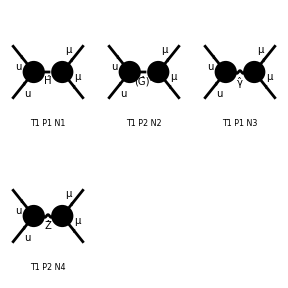

```mathematica
Paint[fieldsBorn];
```

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 3 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 4 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 5 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 6 aebe/cfdf/egfhghgh.m, 0 diagrams

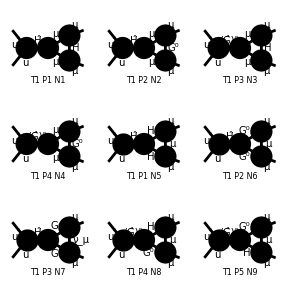

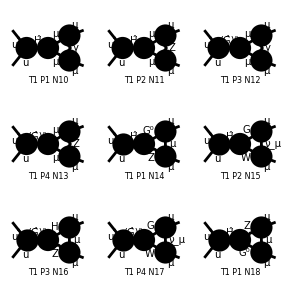

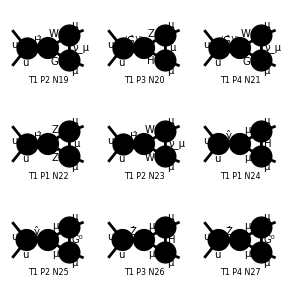

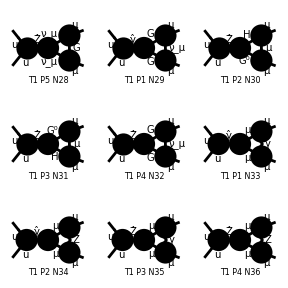

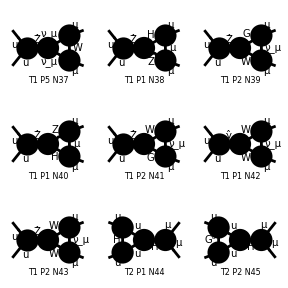

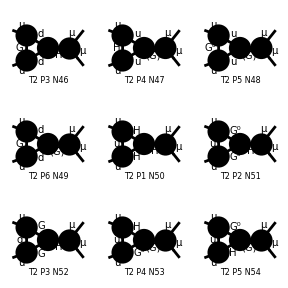

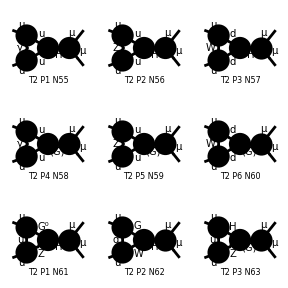

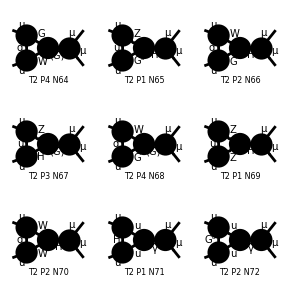

```mathematica
Paint[fields1L];
```

```mathematica
myAmpBorn=ExtractAmplitude[ampBorn];
myAmp1L=ExtractAmplitude[amp1L];
```

```mathematica
zeroOnShellMass={DiracSpinor[p_,MU]->DiracSpinor[p,0]};
```

```mathematica
zeroMass={MU->0,MD->0,mu->0,md->0};
```

```mathematica
SetZeroMassParticles[{MU->0,MD->0,mu->0,md->0}]
```

```mathematica
myAmpBorn=myAmpBorn/.zeroOnShellMass;
myAmp1L=myAmp1L/.zeroOnShellMass;
```

```mathematica
ByteCount[myAmpBorn]
```

14744

```mathematica
ByteCount[myAmp1L]
```

4718880

## Partial Work

```mathematica
loopDiagrams/groupNumber
```

94

```mathematica
inf=(scriptIndex-1)*94+1
sup=scriptIndex*94
```

1

94

```mathematica
myAmpBorn=myAmpBorn;
myAmp1L=Take[myAmp1L,{inf,sup}];
```

```mathematica
SaveAmplitudes[myAmpBorn,"BornAmplitudes.m"];
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/feynArts_amplitudes/BornAmplitudes.m

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/feynArts_amplitudes/OneLoopAmplitudes.m

## Interference

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1/input/kinematics.m.

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
```

```mathematica
smBorn=Sum[AmpSquare[myAmpBorn[[i]],myAmpBorn[[j]]],{i,1,Length[myAmpBorn]},{j,1,Length[myAmpBorn]}];
```

```mathematica
smBorn/.parameterReplace//Simplify
```

1/4 EL^4 ((4 Ql^2 Qu^2 (4 mm^4+(-2+d) s^2-8 mm^2 t+4 s t+4 t^2))/s^2-1/(cw^2 (mz^2-s) s sw^2)2 Ql Qu (-2 I3l Qu sw^2 (4 mm^4+(-2+d) s^2-8 mm^2 t+4 s t+4 t^2)-2 Ql sw^2 (I3u-2 Qu sw^2) (4 mm^4+(-2+d) s^2-8 mm^2 t+4 s t+4 t^2)+I3l I3u (4 mm^4+(-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2-2 mm^2 ((6-5 d+d^2) s+4 t)))+1/(cw^4 (mz^2-s)^2 sw^4)(4 (-2+d) mm^2 Ql s sw^2 (-I3l+Ql sw^2) (I3u^2-2 I3u Qu sw^2+2 Qu^2 sw^4)+Ql^2 sw^4 ((I3u-Qu sw^2)^2 (4 mm^4-(8-6 d+d^2) s^2+2 mm^2 ((8-6 d+d^2) s-4 t)-2 (4-5 d+d^2) s t+4 t^2)+Qu^2 sw^4 (4 mm^4+(-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2-2 mm^2 ((-2+d)^2 s+4 t)))+(I3l-Ql sw^2)^2 (Qu^2 sw^4 (4 mm^4-(8-6 d+d^2) s^2+2 mm^2 ((8-6 d+d^2) s-4 t)-2 (4-5 d+d^2) s t+4 t^2)+(I3u-Qu sw^2)^2 (4 mm^4+(-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2-2 mm^2 ((-2+d)^2 s+4 t)))))

```mathematica
AmpSquare[myAmp1L[[26]],myAmpBorn[[3]]]
```

$Aborted

```mathematica
SquareSimplifyAndSave[myAmp1L,myAmpBorn[[0]][myAmpBorn[[3]]]];
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_17_1.m.

ABISS: Computed contribution 18-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_18_1.m.

ABISS: Computed contribution 19-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_19_1.m.

ABISS: Computed contribution 20-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_20_1.m.

ABISS: Computed contribution 21-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_21_1.m.

ABISS: Computed contribution 22-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_22_1.m.

ABISS: Computed contribution 23-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_23_1.m.

ABISS: Computed contribution 24-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_24_1.m.

ABISS: Computed contribution 25-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/Processes/qq-mm_1L/qq-mm_1//interferences/Contribution_25_1.m.

```mathematica
a=myAmp1L[[26]]/.parameterReplace/.chargeReplace//Simplify
```

-1/(16 π^4)ⅈ v̄[p2,0].(-(ⅈ EL ((-3+4 sw^2) ga[Lor1].om_-+4 sw^2 ga[Lor1].om_+))/(6 cw sw)).u[p1,0] ū[k1,MM].(-(ⅈ EL MM (om_-+om_+))/(2 mw sw)).(MM+gs[q1+k1]).(ⅈ EL ((-1+2 sw^2) ga[Lor2].om_-+2 sw^2 ga[Lor2].om_+))/(2 cw sw).(MM+gs[q1-k2]).(-(ⅈ EL MM (om_-+om_+))/(2 mw sw)).v[k2,MM] FeynAmpDenominator[1/(-MH^2+(q1)^2),1/(-MM^2+(q1+k1)^2),1/(-MM^2+(q1-k2)^2)] 1/(-MZ^2+(k1+k2)^2) (g[Lor1,Lor2]+(k1+k2)[Lor2] ((-(k1)-k2)[Lor1]+(k1+k2)[Lor1] xi_V[20]) 1/((k1+k2)^2-MZ^2 xi_V[20]))

```mathematica
b=myAmpBorn[[3]]/.parameterReplace/.chargeReplace//Simplify
```

v̄[p2,0].(-2/3 ⅈ EL (ga[Lor1].om_-+ga[Lor1].om_+)).u[p1,0] ū[k1,MM].(ⅈ EL (ga[Lor2].om_-+ga[Lor2].om_+)).v[k2,MM] (g[Lor1,Lor2] 1/(k1+k2)^2+(k1+k2)[Lor1] (k1+k2)[Lor2] (-1+xi_bg) 1/(k1+k2)^4)

```mathematica
AmpSquare[a,b]//AbsoluteTiming
```

{689.256,-((ⅈ EL^6 mm^2 KiraPropagator[q1,mh] KiraPropagator[p3+q1,mm] KiraPropagator[-p1-p2+p3+q1,mm] (48 mm^6-144 mm^4 s+120 d mm^4 s-24 d^2 mm^4 s+48 mm^2 s^2-48 d mm^2 s^2+12 d^2 mm^2 s^2-320 mm^6 sw^2+160 mm^2 s^2 sw^2-80 d mm^2 s^2 sw^2+512 mm^6 sw^4-256 mm^2 s^2 sw^4+128 d mm^2 s^2 sw^4-96 mm^4 t+192 mm^2 s t-120 d mm^2 s t+24 d^2 mm^2 s t+640 mm^4 sw^2 t-320 mm^2 s sw^2 t-1024 mm^4 sw^4 t+512 mm^2 s sw^4 t+48 mm^2 t^2-320 mm^2 sw^2 t^2+512 mm^2 sw^4 t^2-4 (-6+3 d-20 sw^2+32 sw^4) (mm^2-s-t) SP[p1,q1]^2-4 (3 d-4 (3-5 sw^2+8 sw^4)) (mm^2-t) SP[p2,q1]^2+48 mm^2 s SP[p3,q1]-320 mm^2 s sw^2 SP[p3,q1]+512 mm^2 s sw^4 SP[p3,q1]+24 s SP[p3,q1]^2-160 s sw^2 SP[p3,q1]^2+256 s sw^4 SP[p3,q1]^2+2 SP[p1,q1] (24 mm^4-96 mm^2 s+60 d mm^2 s-12 d^2 mm^2 s-160 mm^4 sw^2+160 mm^2 s sw^2+256 mm^4 sw^4-256 mm^2 s sw^4-24 mm^2 t+160 mm^2 sw^2 t-256 mm^2 sw^4 t-2 (12 s-3 d s-20 s sw^2+32 s sw^4+2 mm^2 (-15+3 d+40 sw^2-64 sw^4)+4 mm^2 (3-20 sw^2+32 sw^4)+18 t-6 d t) SP[p2,q1]+2 (-3 d s+60 s sw^2-96 s sw^4+mm^2 (6-40 sw^2+64 sw^4)-6 t+40 sw^2 t-64 sw^4 t) SP[p3,q1])-2 SP[p2,q1] (mm^2 (8 mm^2 (3-20 sw^2+32 sw^4)+s (-3 d^2-8 (3-5 sw^2+8 sw^4)+2 d (9-10 sw^2+16 sw^4)))-mm^2 (s (9 d^2+8 (6+5 sw^2-8 sw^4)+d (-42-20 sw^2+32 sw^4))+8 (3-20 sw^2+32 sw^4) t)+2 (s (12-3 d-20 sw^2+32 sw^4)+mm^2 (6-40 sw^2+64 sw^4)-2 (3-20 sw^2+32 sw^4) t) SP[p3,q1])-12 mm^4 SP[q1,q1]-72 mm^2 s SP[q1,q1]+42 d mm^2 s SP[q1,q1]-6 d^2 mm^2 s SP[q1,q1]+48 s^2 SP[q1,q1]-24 d s^2 SP[q1,q1]+3 d^2 s^2 SP[q1,q1]+80 mm^4 sw^2 SP[q1,q1]-80 s^2 sw^2 SP[q1,q1]+20 d s^2 sw^2 SP[q1,q1]-128 mm^4 sw^4 SP[q1,q1]+128 s^2 sw^4 SP[q1,q1]-32 d s^2 sw^4 SP[q1,q1]+24 mm^2 t SP[q1,q1]+60 s t SP[q1,q1]-42 d s t SP[q1,q1]+6 d^2 s t SP[q1,q1]-160 mm^2 sw^2 t SP[q1,q1]+80 s sw^2 t SP[q1,q1]+256 mm^2 sw^4 t SP[q1,q1]-128 s sw^4 t SP[q1,q1]-12 t^2 SP[q1,q1]+80 sw^2 t^2 SP[q1,q1]-128 sw^4 t^2 SP[q1,q1]))/(4608 cw^2 mw^2 π^4 (mz^2-s) s sw^4))}

```mathematica
AmpSquare[myAmpBorn[[3]],myAmpBorn[[3]]]
```

1/s^2 EL^4 gAl^2 gAu^2 (4 mm^4+2 (-2+d) mm^2 s-2 s^2+d s^2+4 s t+4 t^2-2 mm^2 ((-2+d) s+4 t))

```mathematica
??*ABISS*
```

```mathematica
AmpSquare[myAmp1L[[24]],myAmpBorn[[3]]]//AbsoluteTiming
```

{60.0823,1/(16 π^4 s^2)ⅈ EL^6 gAl^2 gAu^2 gHll^2 mm^2 KiraPropagator[q1,mh] KiraPropagator[p3+q1,mm] KiraPropagator[-p1-p2+p3+q1,mm] (16 mm^6-8 mm^2 s^2+4 d mm^2 s^2-32 mm^4 t+16 mm^2 s t+16 mm^2 t^2+4 (-mm^2+s+t) SP[p1,q1]^2+4 (mm^2-t) SP[p2,q1]^2+16 mm^2 s SP[p3,q1]+8 s SP[p3,q1]^2+2 SP[p1,q1] (8 mm^4-8 mm^2 s-8 mm^2 t+(8 mm^2-2 (4 mm^2+s)) SP[p2,q1]+(4 mm^2-6 s-4 t) SP[p3,q1])-2 SP[p2,q1] (mm^2 (8 mm^2+(-2+d) s)-mm^2 ((-2+d) s+8 t)+2 (2 mm^2+s-2 t) SP[p3,q1])-4 mm^4 SP[q1,q1]+4 s^2 SP[q1,q1]-d s^2 SP[q1,q1]+8 mm^2 t SP[q1,q1]-4 s t SP[q1,q1]-4 t^2 SP[q1,q1])}

## Shift

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,376},{j,4}]
```

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,14},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles/kira_input/Contribution_14_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[C0,{mw},1,0,1,0],userIntegral[C0,{mw},1,1,1,-1],userIntegral[C0,{mw},1,-1,1,0],userIntegral[C0,{mw},1,0,1,-1],userIntegral[C0,{mw},1,1,1,-2],userIntegral[C0,{mw},1,1,0,0],userIntegral[C0,{mw},1,0,0,0],userIntegral[C0,{mw},1,1,0,-1],userIntegral[C0,{mw},1,1,-1,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[C0,{mw},0,0,1,0],userIntegral[C0,{mw},0,1,1,-1],userIntegral[C0,{mw},0,1,0,0],userIntegral[C0,{mw},-1,1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[D0,{mm,mh,mz},1,-1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,-2],userIntegral[D0,{mm,mh,mz},1,1,0,0],userIntegral[D0,{mm,mh,mz},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,1,0,-1],userIntegral[D0,{mm,mh,mz},1,1,-1,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[D0,{mm,mh,mz},0,1,1,-1],userIntegral[D0,{mm,mh,mz},0,1,0,0],userIntegral[D0,{mm,mh,mz},-1,1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[D0,{mm,mz,mh},1,-1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,-2],userIntegral[D0,{mm,mz,mh},1,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,0,0],userIntegral[D0,{mm,mz,mh},1,1,0,-1],userIntegral[D0,{mm,mz,mh},1,1,-1,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[D0,{mm,mz,mh},0,1,1,-1],userIntegral[D0,{mm,mz,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[C0,{m1},0,0,1,0]→0,userIntegral[C0,{m1},0,1,0,0]→0,userIntegral[B0,{m1},1,0,0,0]→0,userIntegral[A0,{m1,m2},1,0,1,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[A0,{m1,m2},1,1,1,-1]→((2 mm^2-s-2 t) userIntegral[A0,{m1,m2},0,1,1,0])/(4 mm^2-s)+((2 mm^2+2 t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 mm^2-s)+((-2 mm^4+m1^2 (-s-2 t)+2 m2^2 t-s t+mm^2 (2 m1^2+2 m2^2+2 t)) userIntegral[A0,{m1,m2},1,1,1,0])/(4 mm^2-s),userIntegral[A0,{m1,m2},1,-1,1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,0,1,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(4 mm^4-mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(-56+24 d) m2^2+(12-4 d) s+(-16+16 d) t)+m2^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+m2^2 ((32-16 d) s+(48-16 d) t))) userIntegral[A0,{m1,m2},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((12-8 d) mm^8+(-2+d) m1^2 s t^2+(2-d) m2^2 s t^2+mm^6 ((-20+8 d) m1^2+(-12+8 d) m2^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t)+m2^2 ((2-d) s+(-40+16 d) t))+mm^2 ((6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2)+m2^2 ((8-2 d) s t+(-12+8 d) t^2))) userIntegral[A0,{m1,m2},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((-4+4 d) mm^8+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) m2^2+(8-8 d) t)+m2^4 (4 s t+(-4+4 d) t^2)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+mm^4 ((-4+4 d) m1^4+(-4+4 d) m2^4+(-4+4 d) s t+(-4+4 d) t^2+m2^2 ((-24+8 d) m1^2+16 t)+m1^2 ((-4+4 d) s+(-16+16 d) t))+m2^2 ((8-4 d) s t^2+m1^2 (-4 d s t+(8-8 d) t^2))+mm^2 ((-24+8 d) m2^4 t+(8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2)+m2^2 (-4 d s t+(-24+8 d) t^2+m1^2 ((8-4 d) s+16 t)))) userIntegral[A0,{m1,m2},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[A0,{m1,m2},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},0,0,1,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[A0,{m1,m2},0,1,1,-1]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (2 m2^2-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[A0,{m1,m2},-1,1,1,0]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (-2 m1^2+2 m2^2+2 mm^2-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[C0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[C0,{m1},1,1,1,-1]→((2 mm^2+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 mm^2-s)+((2 mm^2-s-2 t) userIntegral[C0,{m1},0,1,1,0])/(4 mm^2-s)+((-2 mm^4+m1^2 (-s-2 t)-s t+mm^2 (2 m1^2+2 t)) userIntegral[C0,{m1},1,1,1,0])/(4 mm^2-s),userIntegral[C0,{m1},1,-1,1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,0,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,1,1,-2]→((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((12-8 d) mm^8+(-2+d) m1^2 s t^2+mm^6 ((-20+8 d) m1^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t))+mm^2 ((6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2))) userIntegral[B0,{m1},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(12-4 d) s+(-16+16 d) t)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t))) userIntegral[C0,{m1},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+(((-4+4 d) mm^8+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) t)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+mm^4 ((-4+4 d) m1^4+(-4+4 d) s t+(-4+4 d) t^2+m1^2 ((-4+4 d) s+(-16+16 d) t))+mm^2 ((8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2))) userIntegral[C0,{m1},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[C0,{m1},1,1,0,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[C0,{m1},1,0,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[C0,{m1},1,1,0,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},1,1,-1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[C0,{m1},0,1,1,-1]→-1/2 s userIntegral[C0,{m1},0,1,1,0],userIntegral[C0,{m1},-1,1,1,0]→1/2 (-2 m1^2+2 mm^2-s) userIntegral[C0,{m1},0,1,1,0],userIntegral[D0,{m1,m2,m3},1,1,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 mm^2-s)+((2 mm^2-s-2 t) userIntegral[D0,{m1,m2,m3},0,1,1,0])/(4 mm^2-s)+((mm^2+t) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(4 mm^2-s)+1/(4 mm^2-s)(-2 mm^4+m1^2 (-s-2 t)+m2^2 t+m3^2 t-s t+mm^2 (2 m1^2+m2^2+m3^2+2 t)) userIntegral[D0,{m1,m2,m3},1,1,1,0],userIntegral[D0,{m1,m2,m3},1,-1,1,0]→((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+(s userIntegral[D0,{m1,m2,m3},0,0,1,0])/(2 mm^2)+((m1^2 s-m3^2 s+mm^2 (-2 m2^2+2 m3^2+s)) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,0,1,-1]→((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((mm^2-t) userIntegral[D0,{m1,m2,m3},0,0,1,0])/(2 mm^2)+((-mm^4-m1^2 t+m3^2 t+mm^2 (m1^2+m3^2+t)) userIntegral[D0,{m1,m2,m3},1,0,1,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(8 mm^4-2 mm^2 s)+((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+((mm^8 (-8 m2^2+8 m3^2+(12-8 d) s)+(-2+d) m1^2 s^2 t^2+(2-d) m2^2 s^2 t^2+mm^6 ((-20+8 d) m1^2 s+(-2+d) s^2+m3^2 ((-4+2 d) s-16 t)+8 s t+m2^2 ((-8+6 d) s+16 t))+mm^4 (-2 d s^2 t+(-20+8 d) s t^2+m1^2 ((6-3 d) s^2+8 s t)+m2^2 ((2-d) s^2+(-40+12 d) s t-8 t^2)+m3^2 (4 d s t+8 t^2))+mm^2 ((-4+2 d) m3^2 s t^2+(6-3 d) s^2 t^2+m1^2 (-2 d s^2 t+(12-8 d) s t^2)+m2^2 ((8-2 d) s^2 t+(-8+6 d) s t^2))) userIntegral[A0,{m1,m2},1,1,0,0])/((-64+32 d) mm^6 s+(32-16 d) mm^4 s^2+(-4+2 d) mm^2 s^3)+((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[D0,{m1,m2,m3},0,0,1,0])/(8 mm^4-2 mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(-28+12 d) m2^2+(-28+12 d) m3^2+(12-4 d) s+(-16+16 d) t)+m2^2 ((-2+d) s^2-4 s t+(4-4 d) t^2)+m3^2 ((-2+d) s^2-4 s t+(4-4 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+m2^2 ((16-8 d) s+(24-8 d) t)+m3^2 ((16-8 d) s+(24-8 d) t))) userIntegral[D0,{m1,m2,m3},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+((mm^8 (8 m2^2-8 m3^2+(12-8 d) s)+(-2+d) m1^2 s^2 t^2+(2-d) m3^2 s^2 t^2+mm^6 ((-20+8 d) m1^2 s+(-2+d) s^2+m2^2 ((-4+2 d) s-16 t)+8 s t+m3^2 ((-8+6 d) s+16 t))+mm^4 (-2 d s^2 t+(-20+8 d) s t^2+m1^2 ((6-3 d) s^2+8 s t)+m3^2 ((2-d) s^2+(-40+12 d) s t-8 t^2)+m2^2 (4 d s t+8 t^2))+mm^2 ((-4+2 d) m2^2 s t^2+(6-3 d) s^2 t^2+m1^2 (-2 d s^2 t+(12-8 d) s t^2)+m3^2 ((8-2 d) s^2 t+(-8+6 d) s t^2))) userIntegral[D0,{m1,m2,m3},1,0,1,0])/((-64+32 d) mm^6 s+(32-16 d) mm^4 s^2+(-4+2 d) mm^2 s^3)+(((-4+4 d) mm^8 s+(-2+d) m2^4 s t^2+(-2+d) m3^4 s t^2+(-2+d) s^3 t^2+mm^6 (4 m2^4+4 m3^4+(8-8 d) m1^2 s+(4-4 d) m2^2 s+m3^2 (-8 m2^2+(4-4 d) s)+(8-8 d) s t)+m1^4 ((-2+d) s^3+(-4+4 d) s^2 t+(-4+4 d) s t^2)+m1^2 (2 d s^3 t+(-4+4 d) s^2 t^2)+m2^2 ((4-2 d) s^2 t^2+m1^2 (-2 d s^2 t+(4-4 d) s t^2))+m3^2 ((4-2 d) s^2 t^2+m1^2 (-2 d s^2 t+(4-4 d) s t^2)+m2^2 (4 s^2 t+2 d s t^2))+mm^4 ((-4+4 d) m1^4 s+m2^4 ((-2+d) s-8 t)+m3^4 ((-2+d) s-8 t)+(-4+4 d) s^2 t+(-4+4 d) s t^2+m2^2 ((-12+4 d) m1^2 s+8 s t)+m1^2 ((-4+4 d) s^2+(-16+16 d) s t)+m3^2 ((-12+4 d) m1^2 s+8 s t+m2^2 (2 d s+16 t)))+mm^2 ((8-4 d) s^2 t^2+m1^4 ((8-4 d) s^2+(8-8 d) s t)+m2^4 (2 d s t+4 t^2)+m3^4 (2 d s t+4 t^2)+m1^2 (-8 d s^2 t+(8-8 d) s t^2)+m2^2 (-2 d s^2 t+(-12+4 d) s t^2+m1^2 ((4-2 d) s^2+8 s t))+m3^2 (-2 d s^2 t+(-12+4 d) s t^2+m1^2 ((4-2 d) s^2+8 s t)+m2^2 ((-24+4 d) s t-8 t^2)))) userIntegral[D0,{m1,m2,m3},1,1,1,0])/((-32+16 d) mm^4 s+(16-8 d) mm^2 s^2+(-2+d) s^3),userIntegral[D0,{m1,m2,m3},1,1,0,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[D0,{m1,m2,m3},1,0,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[D0,{m1,m2,m3},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 (2 m2^2-2 m3^2+s)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[D0,{m1,m2,m3},0,1,1,-1]→1/2 userIntegral[A0,{m1,m2},0,1,0,0]+1/2 userIntegral[D0,{m1,m2,m3},0,0,1,0]+1/2 (m2^2+m3^2-s) userIntegral[D0,{m1,m2,m3},0,1,1,0],userIntegral[D0,{m1,m2,m3},0,1,0,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[D0,{m1,m2,m3},-1,1,1,0]→1/2 userIntegral[A0,{m1,m2},0,1,0,0]+1/2 userIntegral[D0,{m1,m2,m3},0,0,1,0]+1/2 (-2 m1^2+m2^2+m3^2+2 mm^2-s) userIntegral[D0,{m1,m2,m3},0,1,1,0],userIntegral[B0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[B0,{m1},1,1,1,-1]→((2 mm^2-s-2 t) userIntegral[B0,{m1},0,1,1,0])/(4 mm^2-s)+((2 mm^2+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 mm^2-s)+((-2 mm^4+2 m1^2 t-s t+mm^2 (2 m1^2+2 t)) userIntegral[B0,{m1},1,1,1,0])/(4 mm^2-s),userIntegral[B0,{m1},1,-1,1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,0,1,-1]→((mm^2-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4+m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-56+24 d) m1^2+(12-4 d) s+(-16+16 d) t)+m1^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((32-16 d) s+(48-16 d) t))) userIntegral[B0,{m1},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+(((12-8 d) mm^8+(2-d) m1^2 s t^2+mm^6 ((-12+8 d) m1^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((2-d) s+(-40+16 d) t))+mm^2 ((6-3 d) s t^2+m1^2 ((8-2 d) s t+(-12+8 d) t^2))) userIntegral[B0,{m1},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((-4+4 d) mm^8+(8-4 d) m1^2 s t^2+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) t)+m1^4 (4 s t+(-4+4 d) t^2)+mm^4 ((-4+4 d) m1^4+16 m1^2 t+(-4+4 d) s t+(-4+4 d) t^2)+mm^2 ((-24+8 d) m1^4 t+(8-4 d) s t^2+m1^2 (-4 d s t+(-24+8 d) t^2))) userIntegral[B0,{m1},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[B0,{m1},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4+m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,1,-1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},0,0,1,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},0,1,1,-1]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2-s) userIntegral[B0,{m1},0,1,1,0],userIntegral[B0,{m1},0,1,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},-1,1,1,0]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2+2 mm^2-s) userIntegral[B0,{m1},0,1,1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[C0,{mw},1,0,1,0],userIntegral[C0,{mw},1,1,1,-1],userIntegral[C0,{mw},1,-1,1,0],userIntegral[C0,{mw},1,0,1,-1],userIntegral[C0,{mw},1,1,1,-2],userIntegral[C0,{mw},1,1,0,0],userIntegral[C0,{mw},1,0,0,0],userIntegral[C0,{mw},1,1,0,-1],userIntegral[C0,{mw},1,1,-1,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[C0,{mw},0,0,1,0],userIntegral[C0,{mw},0,1,1,-1],userIntegral[C0,{mw},0,1,0,0],userIntegral[C0,{mw},-1,1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[D0,{mm,mh,mz},1,-1,1,0],userIntegral[D0,{mm,mh,mz},1,0,1,-1],userIntegral[D0,{mm,mh,mz},1,1,1,-2],userIntegral[D0,{mm,mh,mz},1,1,0,0],userIntegral[D0,{mm,mh,mz},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,1,0,-1],userIntegral[D0,{mm,mh,mz},1,1,-1,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[D0,{mm,mh,mz},0,1,1,-1],userIntegral[D0,{mm,mh,mz},0,1,0,0],userIntegral[D0,{mm,mh,mz},-1,1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[D0,{mm,mz,mh},1,-1,1,0],userIntegral[D0,{mm,mz,mh},1,0,1,-1],userIntegral[D0,{mm,mz,mh},1,1,1,-2],userIntegral[D0,{mm,mz,mh},1,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,0,0],userIntegral[D0,{mm,mz,mh},1,1,0,-1],userIntegral[D0,{mm,mz,mh},1,1,-1,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[D0,{mm,mz,mh},0,1,1,-1],userIntegral[D0,{mm,mz,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,14},{j,1}]
```

```mathematica
Transliterate
```

abck.12.14

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,14}]
```

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
minorReplace1={gAl->-Ql,gAu->-Qu,gAd->-Qd};
minorReplace2={gZlL->(I3l-Ql*sw^2)/(cw*sw),gZlR->(-Ql*sw^2)/(cw*sw),gZNL->(I3N)/(cw*sw),gZuL->(I3u-(Qu*sw^2))/(cw*sw),gZuR->(-Qu*sw^2)/(cw*sw),gZdL->(I3d-(Qd*sw^2))/(cw*sw),gZdR->(-Qd*sw^2)/(cw*sw)};
```

```mathematica
coefficients=Plus@@diagramCoefficients //Simplify
```

diagramCoefficients

```mathematica
Length[coefficients]
```

34

```mathematica
Do[
coefficients[[i]]>>(NotebookDirectory[]<>"totalcoeff/Coefficients_"<>ToString[i]<>"_1.m"),
{i,Length[coefficients]}]
```

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m")
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
masters=DeleteDuplicates[masters]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[C0,{mw},1,1,1,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[C0,{mw},0,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[D0,{mm,mh,mz},1,0,1,0],userIntegral[A0,{mm,mh},1,1,0,0],userIntegral[D0,{mm,mh,mz},0,1,1,0],userIntegral[D0,{mm,mh,mz},1,1,1,0],userIntegral[A0,{mm,mh},1,0,0,0],userIntegral[D0,{mm,mh,mz},0,0,1,0],userIntegral[A0,{mm,mh},0,1,0,0],userIntegral[D0,{mm,mz,mh},1,0,1,0],userIntegral[A0,{mm,mz},1,1,0,0],userIntegral[D0,{mm,mz,mh},0,1,1,0],userIntegral[D0,{mm,mz,mh},1,1,1,0],userIntegral[A0,{mm,mz},1,0,0,0],userIntegral[D0,{mm,mz,mh},0,0,1,0],userIntegral[A0,{mm,mz},0,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Length[masters]
```

34

```mathematica
userIntegralMasses[A0]
```

{M1,M2,M2,0}

```mathematica
userLoopMomenta
```

{q1}

```mathematica
userPropagatorMomenta[A0]
```

{q1,p3+q1,-p1-p2+p3+q1,-p1+p3+q1}

```mathematica
userIntegralFamiliesNames
```

{A0,B0,C0,D0}

```mathematica
Do[If[sameIntegral[masters[[i]],masters[[j]]&&i<j],
Print[ToString[i]<>" "<>ToString[j]]
]
,{i,Length[masters]},{j,Length[masters]}]
```

3 9

3 33

4 6

9 33

19 26

19 34

26 34

```mathematica
masters[[19]]
masters[[26]]
masters[[34]]
```

userIntegral[A0,{mm,mh},1,0,0,0]

userIntegral[A0,{mm,mz},1,0,0,0]

userIntegral[A0,{mm,m2},1,0,0,0]

## Analogous Integral Families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
]
```

## Functions

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
]
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}]
```